# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,maxran_,limit_,label_,epilog_:{}]:=Module[{funplot,epsplot},
funplot=DiscretePlot[fun[n],{n,0,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{0,limit},{maxran,limit}}],Arrow[{{(*maxran-20*)20,limit+.05},{(*maxran-25*)15,limit}}],Text["lim_(n → ∞) a_n="<>ToString[limit],{(*maxran-20*)22,limit+.05},Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,.2},0.0001,.2,Appearance->"Open" },SaveDefinitions->True
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,maxran_,limit_,label_,epilog_:{}]:=Module[{funplot,epsplot},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,.2},0.0001,.2,Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,0,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{{Line[{{0,limit},{maxran,limit}}],Arrow[{{(*maxran-20*)20,limit+.05},{(*maxran-25*)15,limit}}],Text["lim_(n → ∞) a_n="<>ToString[limit],{(*maxran-20*)22,limit+.05},Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}]}
]
]
```

# 1) Polynomials

Satz 4.1.: Ist p(z) ein Polynom vom Grad n∈ℕ und z_0 eine Nullstelle von p, also p(z_0)=0, dann gibt es ein Polynom q(z) vom Grad n-1 mit p(z)=(z-z_0)q(z).

Prove by mathematical induction...

## Solution

Initial step: n=1

p(z)=α_0+α_1 z

We can rewrite the polynomial as p(z)=α_0+α_1 z=α_1(z-(-α_0/α_1))  and so we can take z_0=-α_0/α_1 to finish the proof for n=1.

induction step: we assume validity for n-1 to prove the same for n

p(z)=∑_(j=0)^n α_j z^j

As suggested in the Übungsblatt, we subtract a polynomial of the form (z-z_0) z^(n-1) from p(z):

p(z) -α_n(z-z_0) z^(n-1)= ∑_(j=0)^(n-1) α_j z^j+α_n z^n-α_n(z-z_0) z^(n-1)=∑_(j=0)^(n-1) α_j z^j+α_n z_0 z^(n-1)

The maximum power of z on the right-hand side (RHS) is n-1  and the RHS is thus a polynomial of degree n-1, for which we can use Satz 4.1. Therefore:

∑_(j=0)^(n-1) α_j z^j+α_n z_0 z^(n-1)=(z-z_0)q̄(z), where q̄(z)=∑_(j=0)^(n-2) β_j z^j is a polynomial of degree n-2. This is the induction step.

We can rewrite the whole equation as:

p(z) -α_n(z-z_0) z^(n-1)=(z-z_0)∑_(j=0)^(n-2) β_j z^j and so

p(z)=α_n(z-z_0) z^(n-1)+(z-z_0)∑_(j=0)^(n-2) β_j z^j=(z-z_0)(α_n z^(n-1)+∑_(j=0)^(n-2) β_j z^j) .

The expression on the RHS is a polynomial of degree n-1 and we can thus define q(z)=α_n z^(n-1)+∑_(j=0)^(n-2) β_j z^j to conclude

p(z)=(z-z_0)q(z) as was to be shown.

# 2) Sequence

a_n=(n^2-n)/(2 n^2+3)

Monotonic? Bounded?

## Plot

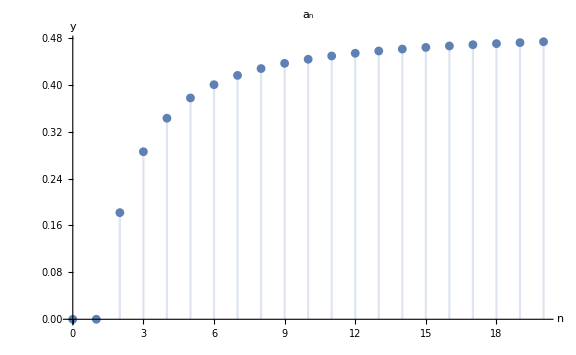

```mathematica
discPlotFun[(n^2-n)/(2 n^2+3),{0,20},{{0,20},All},{},"a_n"]
```

## Solution

Since a_(n+1)-a_n=((n+1)^2-(n+1))/(2(n+1)^2+3)-(n^2-n)/(2 n^2+3)=(2 (4 n+n^2))/((3+2 n^2) (5+4 n+2 n^2))>0, we get a_(n+1)>a_n. The sequence is therefore monotonically increasing.

The sequence is bounded from below as a_n=(n^2-n)/(2 n^2+3)=(n(n-1))/(2 n^2+3)≥0.

Is the sequence bounded from above? Let’s say the bound is 1. Is a_n=(n^2-n)/(2 n^2+3)<1?

(n^2-n)/(2 n^2+3)<1⇔n^2-n<2 n^2+3⇔0<n^2+n+3

Expression n^2+n+3 is indeed always positive (there are no real solutions to n^2+n+3=0). Therefore a_n<1 and the sequence a_n is bounded from above.

# 3) Limit

a_n=(n^2-n)/(2 n^2+3)

lim_(n→∞) a_n=?

## Solution

Sequence a_n is bounded and monotonic → limit (Grenzwert) exists.

lim_(n→∞) a_n=lim_(n→∞) (n^2-n)/(2 n^2+3)=lim_(n→∞) (n^2(1-1/n))/(n^2(2+3/n^2))=lim_(n→∞) (1-1/n)/(2+3/n^2)=1/2

Or by definition: At first, we see in the plot above, that a_n approaches 1/2 for large n. We then guess that the limit is indeed 1/2 and use the definition of the limit to really prove it is so.

We want to show, that: (∀ϵ>0)(∃n_0∈ℕ)(∀n∈ℕ, n>n_0)(|a_n-1/2|<ϵ)

|a_n-1/2|=|(n^2-n)/(2 n^2+3)-1/2|=|(-2 n-3)/(2 (2 n^2+3))|=(2 n+3)/(2 (2 n^2+3))<ϵ

(2 n+3)/(2 (2 n^2+3))<ϵ⇔2 n+3<2ϵ (2 n^2+3)⇔0<4ϵ n^2-2n+6ϵ-3   ...(⋆)

There are many ways how we can determine n_0, one of them is to directly solve the formula above:

Roots of the quadratic function on the RHS of (⋆) (general formula n_(1,2)=(-b±√(b^2-4 a c))/(2a)): n_(1,2)=(2±√(4-4 4ϵ (6ϵ-3)))/(8 ϵ)=(1±√(1-24 ϵ^2 +12ϵ))/(4 ϵ).

So for given ϵ we can set n_0:=⌈(1+√(1-24 ϵ^2 +12ϵ))/(4 ϵ)⌉∈ℕ.

Another possibility is for example  n_0:=⌈1/ϵ⌉.

## Graphically

## The first choice: n_0=⌈(1+√(1-24 ϵ^2 +12ϵ))/(4 ϵ)⌉

```mathematica
plotLimitDisc[(#1^2-#1)/(2 #1^2+3)&,Ceiling[(1+√(1+12 #-24 #^2))/(4 #)]&,100,.5,"Sequence a_n, its limit 1/2 and varying ϵ"]
```

## The second choice: n_0=⌈1/ϵ⌉

```mathematica
plotLimitDisc[(#1^2-#1)/(2 #1^2+3)&,Ceiling[1/#]&,100,.5,"Sequence a_n, its limit 1/2 and varying ϵ"]
```

# 4) Another sequence and limit

a_n=x^(2n),  0<x<1

Monotonically decreasing? Convergent? Limit?

## Plot

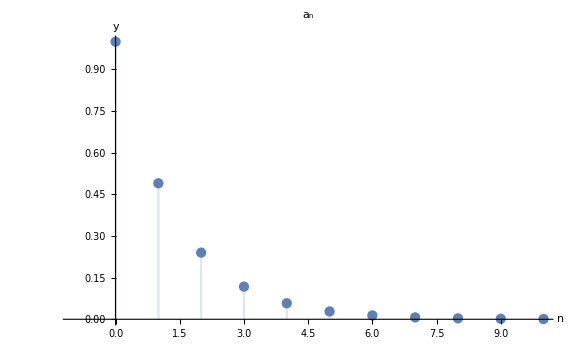

```mathematica
discPlotFun[With[{x=.7},x^(2n)],{0,10},{{-1,10},All},{},"a_n"]
```

## Solution

Since (a_(n+1))/a_n=x^(2(n+1))/x^(2n)=x^2<1, we get a_(n+1)<a_n. The sequence is therefore monotonically decreasing.

As 0<x<1, we have 0<x^(2n)<1 and a_n is bounded. Therefore, a_n is convergent.

lim_(n→∞) a_n=0 ?

We want to show, that: (∀ϵ>0)(∃n_0∈ℕ)(∀n∈ℕ, n>n_0)(|a_n|<ϵ)

|a_n|<ϵ⇔x^(2n)<ϵ⇔2n ln(x)>ln(ϵ)⇔n >1/2(ln(ϵ))/(ln(x))

So for given ϵ we can set n_0:=⌈1/2(ln(ϵ))/(ln(x))⌉∈ℕ.

# 5) Fibonacci sequence

a_1=a_2=1
a_(n+2)=a_(n+1)+a_n,   n≥1

a_n=1/(√5)(((1+√5)/2)^n-((1-√5)/2)^n)

Prove by mathematical induction. Monotonic? Convergent? Approximation?

## Plot

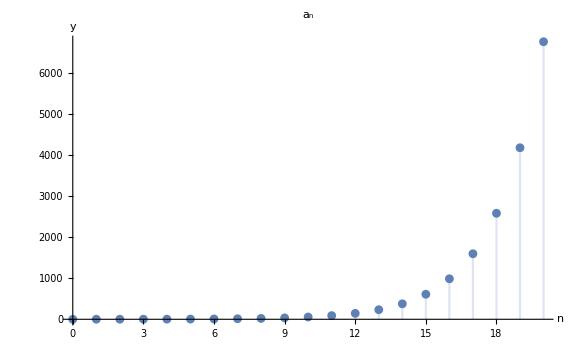

```mathematica
discPlotFun[1/(√5)(((1+√5)/2)^n-((1-√5)/2)^n),{0,20},{{0,20},All},{},"a_n"]
```

## Solution

## Formula

Initial step: n=1 and n=2

a_1=1/(√5)(((1+√5)/2)^1-((1-√5)/2)^1)=1
a_2=1/(√5)(((1+√5)/2)^2-((1-√5)/2)^2)=1

induction step: we assume validity for n and n+1 to prove the same for n+2

a_(n+2)=1/(√5)(((1+√5)/2)^(n+2)-((1-√5)/2)^(n+2)) ?

a_(n+1)+a_n=1/(√5)(((1+√5)/2)^(n+1)-((1-√5)/2)^(n+1))+1/(√5)(((1+√5)/2)^n-((1-√5)/2)^n)=1/(√5)(((1+√5)/2)^n((1+√5)/2+1)-((1-√5)/2)^n((1-√5)/2+1))=1/(√5)(((1+√5)/2)^n((3+√5)/2)-((1-√5)/2)^n((3-√5)/2))=1/(√5)(((1+√5)/2)^n((1+√5)/2)^2-((1-√5)/2)^n((1-√5)/2)^2)=1/(√5)(((1+√5)/2)^(n+2)-((1-√5)/2)^(n+2))=a_(n+2)

## Monotonicity, convergence and approximation

a_(n+2)>a_(n+1) ?

a_(n+2)-a_(n+1)=a_n>0 ⇒  a_(n+2)>a_(n+1) ⇒ monotonically increasing

Not bounded, therefore divergent.

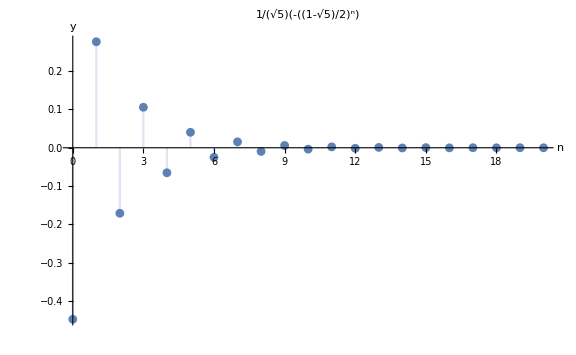

```mathematica
discPlotFun[1/(√5)(-((1-√5)/2)^n),{0,20},{{0,20},All},{},"1/(√5)(-((1-√5)/2)^n)"]
```

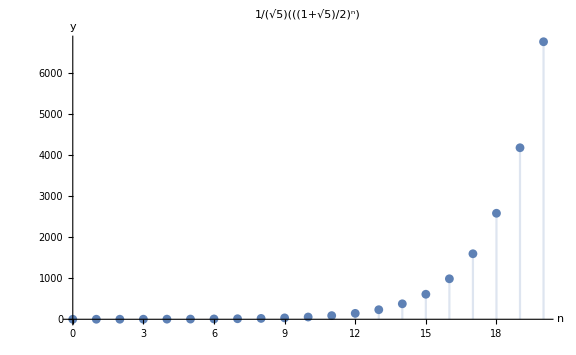

```mathematica
discPlotFun[1/(√5)(((1+√5)/2)^n),{0,20},{{0,20},All},{},"1/(√5)(((1+√5)/2)^n)"]
```

For n≫1 approximately a_n≈1/(√5)(((1+√5)/2)^n .

# 6) Population

a_0=10
a_1=12
a_(n+2)=1.2 a_(n+1)-0.001 a_n^2,   n≥0

Significance of  -0.001 a_n^2 ?

## Plot

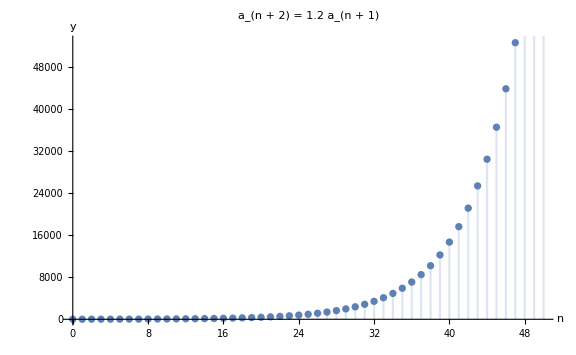

```mathematica
ClearAll[b]
b[0]=10;
b[1]=12;
b[n_]:=b[n]=1.2 b[n-1];

Framed@DiscretePlot[b[n],{n,0,50},PlotLabel->Style["a_(n + 2) = 1.2 a_(n + 1)",Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]
```

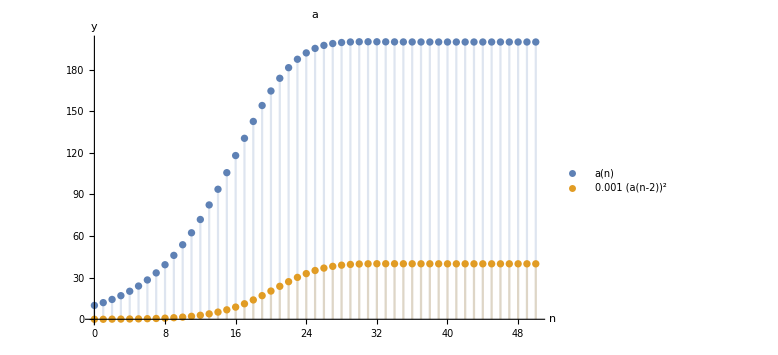

```mathematica
ClearAll[a]
a[-2]=0;
a[-1]=0;
a[0]=10;
a[1]=12;
a[n_]:=a[n]=1.2 a[n-1]-0.001 a[n-2]^2;

Framed@DiscretePlot[{a[n],0.001 a[n-2]^2},{n,0,50},PlotLabel->Style["a",Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20},PlotLegends->"Expressions"]
```